```mathematica
dynamicNewtonPic[fIn_, {var_,varMin_,varMax_}, resolution_, bail_: 50] := Module[
	{f, n, limitInfo, color, colors, roots, preColors, step, limitData, 
	 r, xmin,xmax,ymin,ymax, z, pic},

	f = Function[var, fIn]; (* A very standard example *)
	n = Function[var, Evaluate[Simplify[var - f[var]/f'[var]]]];

	r = 0.01;
	limitInfo = With[{bailLoc = bail, rLoc = r, fLoc = f, nLoc = n},
	   Compile[{{z0, _Complex}},
		Module[{zz, cnt},
		 cnt = 0; zz = z0;
		 While[Abs[fLoc[zz]] > rLoc && cnt < bailLoc,
		  zz = nLoc[zz];
		  cnt = cnt + 1
		  ];
		 {zz, cnt}],
		RuntimeAttributes -> {Listable},
		Parallelization -> True,
		RuntimeOptions -> "Speed"
		]];

	xmin=Re[varMin];
	xmax=Re[varMax];
	ymin=Im[varMin];
	ymax=Im[varMax];
	step = Max[xmax-xmin,ymax-ymin]/(resolution+1);
	limitData = limitInfo[
	  ParallelTable[x + I*y, {y, ymax,ymin, -step}, {x, xmin,xmax, step}]];
	roots = z /. NSolve[f[z] == 0, z];
	preColors = List @@@ Table[ColorData[61, k], {k, 1, Length[roots]}];
	preColors = Append[preColors, {0.0, 0.0, 0.0}];
	color = With[{bailLoc = bail, rootsLoc = roots, preColorsLoc = preColors},
	   Compile[{{z, _Complex}, {cnt, _Complex}},
		Module[{arg, time, i},
		 arg = Arg[z];
		 time = Abs[cnt];
		 i = 1;
		 Scan[If[Abs[z - #] < 0.1, Return[i], i++] &, rootsLoc];
		 Abs[preColorsLoc[[i]]*(cnt/bailLoc)^(N[1/9])]
		 (* The exponent 0.2 adjusts the brightness of the image. *)]]
	];
	colors = Apply[color, limitData, {2}];
	pic = Graphics[Raster[colors,{{xmin,ymin},{xmax,ymax}}], 
		ImageSize -> 3/step,Frame->True];
	Panel[DynamicModule[{pt={0,0}},
		LocatorPane[Dynamic[pt],
			Show[{pic,
				Graphics[{Thick,Purple,Dynamic[Line[{Re[#],Im[#]}& /@
					NestWhileList[n,pt[[1]]+pt[[2]]*I,0.01<Abs[#]<10&,1,100]]]}]},
				PlotRange -> {{xmin,xmax},{ymin,ymax}},
				ImageSize -> resolution
			]
		]
	]]
];
```

```mathematica
(* new Salem Polynomial: Spider Salem *)
```

```mathematica
f[x_]=(1+4 z-10 z^3-13 z^4-16 z^5-19 z^6-22 z^7+28 z^9+31 z^10)
```

1+4 z-10 z^3-13 z^4-16 z^5-19 z^6-22 z^7+28 z^9+31 z^10

```mathematica
g1=dynamicNewtonPic[f[z],{z,-2-2*I,2+2*I},2000];
```

```mathematica
g2=dynamicNewtonPic[f[z],{z,-1.2-1.2*I,1.2+1.2*I},2000];
```

```mathematica
g3=dynamicNewtonPic[f[z],{z,-0.75-0.75*I,0.75+0.75*I},2000];
```

```mathematica
g4=dynamicNewtonPic[f[z],{z,-0.45-0.45*I,0.45+0.45*I},2000];
```

```mathematica
Export["dynamicNewtonPic_New_Salem_decic_2000res_lt9th_grid.jpg",Rasterize[GraphicsGrid[{{g1,g2},{g3,g4}}],"Image",ImageSize->4000]];
```

```mathematica
(*end*)
```

## Mahler Measure of New Salem Polynomial

```mathematica
.10(*https://mathworld.wolfram.com/LehmersMahlerMeasureProblem.html*)
```

```mathematica
RandomPolynomial[x_,n_,r_List]:=Nest[#x+Random[Integer,r]&,0,n+1]

MahlerMeasure[p_Integer,x_]:=0
NMahlerMeasure[p_Integer,x_]:=0

MahlerMeasure[p_,x_]:=Module[{roots=x/.{ToRules[Roots[p==0,x]]}},
Abs[Function[x,p][0]] Times@@(Max[Abs[#],1]&/@roots)
]

NMahlerMeasure[p_,x_]:=Module[{roots=x/.{ToRules[NRoots[p==0,x]]}},
Abs[Function[x,p][0]] Times@@(Max[Abs[#],1]&/@roots)
]

NMahlerMeasure2[p_,x_]:=Exp[NIntegrate[Log[Abs[p/.x->Exp[2Pi I t]]],{t,0,1}]]
```

```mathematica
(*Using the MathWorld code for the Mahler Measure*)
```

```mathematica
lehmer[z_]:=(1+4 z-10 z^3-13 z^4-16 z^5-19 z^6-22 z^7+28 z^9+31 z^10)
```

```mathematica
{#,N[#]}&@(m=MahlerMeasure[lehmer[x],x])
```

{Root1.06Root[1+4 #1-10 #1^3-13 #1^4-16 #1^5-19 #1^6-22 #1^7+28 #1^9+31 #1^10&,4]1.0645673266763072,1.06457}

```mathematica
(*roots of the new Salem polynomial*)
```

```mathematica
(* The roots the polynomial seems to be both Salem and Pisot*)
```

```mathematica
(* The new Polynomial breaks the rule of the highest power (z^10) coefficient being one: it is the Prime 31 instead*)
```

```mathematica
v=z/.NSolve[lehmer[z]==0,z]
```

{-0.743848-0.456798 ⅈ,-0.743848+0.456798 ⅈ,-0.613487,-0.355586-0.757408 ⅈ,-0.355586+0.757408 ⅈ,-0.297403,0.31961-0.719094 ⅈ,0.31961+0.719094 ⅈ,0.502743,1.06457}

```mathematica
(*inversion polynomial*)
```

```mathematica
ExpandAll[z^10*lehmer[1/z]]
```

31+28 z-22 z^3-19 z^4-16 z^5-13 z^6-10 z^7+4 z^9+z^10

```mathematica
u=z/.NSolve[ExpandAll[z^10*lehmer[1/z]]==0,z]
```

{-3.36244,-1.63003,-0.976212-0.599493 ⅈ,-0.976212+0.599493 ⅈ,-0.507901-1.08184 ⅈ,-0.507901+1.08184 ⅈ,0.516128-1.16124 ⅈ,0.516128+1.16124 ⅈ,0.939349,1.98909}

```mathematica
(*four real and 6 complex: all but one less than one *)
```

```mathematica
Table[Abs[v[[i]]],{i,Length[v]}]
```

{0.872911,0.872911,0.613487,0.836725,0.836725,0.297403,0.786922,0.786922,0.502743,1.06457}

```mathematica
Table[Abs[u[[i]]],{i,Length[u]}]
```

{3.36244,1.63003,1.14559,1.14559,1.19514,1.19514,1.27077,1.27077,0.939349,1.98909}

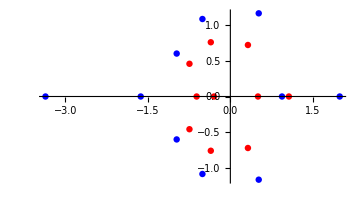

```mathematica
ComplexListPlot[{v,u},PlotStyle->{Red,Blue},ImageSize->Medium]
```

```mathematica
CoefficientList[lehmer[z],z]
```

{1,4,0,-10,-13,-16,-19,-22,0,28,31}

```mathematica
w=CoefficientList[Normal[Series[1/ExpandAll[z^10*lehmer[1/z]],{z,0,100}]],z];
```

```mathematica
(*Integer sequence generated in powers of 31 by the new Salem polynomial*)
```

```mathematica
Table[31^i*w[[i]],{i,Length[w]}]
```

{1,-28,784,-810,-3267,15594328,-51557913,10954740430,52431777945,9465440163940,228496039409971,3990016476287110,381192874454647522,3942033210500199104,306802964594315076607,8855252683413864955688,243157357527835597709178,10586358759944697023361548,266313168536112167553906430,11050268712581227073118189528,312409330832416014953683498562,11080760516443764806620419807620,376093709136416991304430425661190,11211386285489458114151291305016648,415214312877984470855564354889028643,12626209739541162792590016562704553912,431908934440640784781372218308496121086,14296494105132124681007081064762847334582,460904448439718119621189719141139837201831,15660759438855749533764503350678700535683708,502770102221013360206928869881154185986596053,16949353807219533022637681204785834045988487198,553266310471935365483472663226420945127115648619,18254138767141662257714394576072931390730430251008,607586071442391456756597837599937104629286657797769,19819503984935129143171916085380776205652213056279174,660514369498810347582721377031674939073318926927881908,21678700282252792000056368787330466685117881412368310188,716387365303267555186140734321534318936529702575784874397,23676826822455282197277738803574797741660306203040763670784,779129916775544941897706962956011935789322443954880745127732,25794092475105632763265695617024570843648856267913399569585096,848993729689500022651136519842348776817010419019930423510574204,28062885436497975792304866055956466747967014714405984634500924000,925788501394386995964720234812976326813246209262408327047230183940,30532810952609325359337877892007227684738621095777636579074514759480,1008770513278459439518726298187173400973649153377668039742538877971788,33254516900060412260152059646156283409738580475160598570166325949623872,1098273081232829865372949337796547286482346133686184448998318407726414853,36233206485216093107869051864757898048415784791972306372880964775816944700,1195713697108386485803944433601522387525042760136351798188083063959495054060,39470353277273716155153285406248818721222190480195454175380417166470611564870,1302144466207156824106607054341536114743266529679689056794288626448167159840529,42986379735956431523366400017378105443218478346129142731058973797065985467243472,1418313294660683364353481043542559623086041715855916924558777166889241442586290563,46810487933186363291798345757776621354933215134692948558580487318578080035013669662,1544872206618284210217810580748605343462912604133879124171775926993402528729353870973,50977991874664978099735206701740342966478511423030114944228351070590715785922441425740,1682552991434067059426463812752261797390780613052323018282677263686859715426472849795167,55521731932880061738339939659911186282817774937648170482112163695162341623765690167692342,1832400391476199504355263440251464044285902021177061914486839078449628338924383822433469702,60471427897241413087394045223361920009231083545744145651060185402135746034585951120416282056,1995616938743291899458832132449555797262670109380567626408462890948912245004201805154419691131,65860736959995273105549550891514948080280490991982431406365876858963557498042919655187020962952,2173431553102565006933688193235495867713196030821918936489064379736876505202724927523220989891246,71728653662590785740585378095799426350880067788637173187224648726025793125045951375795773118419252,2367126360708609373089483958935939465324518876996466677037003550219817715255697223263581631898167546,78118983232348554654060798362126203950550677406487258892411551909685163048799093862497981125619521688,2578072108122482546095974482493546793754094454323440588289797147863995167232200742639843011835828778694,85079448972907763209016121596481155250465764351306791237886633309295665436259669571343055114478325178140,2807787663370415159258332716704809096017441056115656931348191980833144130456749529634631128492011117851474,92660774421196738738281404279210497483676340072173541933240632064738632221306471297426366288437137187433960,3057961536777880669927136463604623616788573734630085474504013496846791964502251639366270310905675024348594983,100917660459992700276578844561690920045506294331854722888724288890157758061706685649487331550983098795158986096,3330432811046449081751081768169560079083631447758284419614847051937886667573247082197170276185361089510671150426,109909987535411304568774999324810355266058858180167537859737571861547581925431213202177275931693891706586374980486,3627192067113576770017175973484827591069484838817734400053061212229375013698268992087083907504130140816137345800955,119703337209097408505526544782904938830608951340203999008827935895941712233474129418210442018210458186236403110615380,3950397814557250388624745476098879289681656922047197136175857216893163834767177141327616435748456476142852618734014577,130369325655308535373287774475540692263770837206952169537153737264649334782377369226500178913251225895017431452627950286,4302399601347706685930462652420199239137831741515886570146643889931782778861314716526175653367893037627666759863473210447,141985841895467618267287168037158651454897549876500228993532726937451201434677438179873609657964767324330129344569408497224,4685762512616326061825352590011177183601546007651347957276230098536877441220071356635191067964982891692175136650324295481141,154637523520777612847791106898029082259764250020051600397979847346992465035603665220799468630815251448658384569069125807857302,5103284042437282503414217029650087708921792172699260715580961610439352061983242943801152222151770344326435649444215157364922712,168416513556667650742541346015247912461088567713045492839817584970921234754704174459824194969233452432599033455405003616957954836,5558010103572208436649386759360249616373754702662444933787742263790867539380894883702922424428644667346083685955763168904856236825,183423224090750314873267008123035309877321479511995670018342132318867898900686895038581127553581203699174295047782476834526290642112,6053255886976845296723310691541615557546671948954100219546919095195594808793028432606147298238063409296714616726289608769073740838248,199767075218485054048351847746087089796219051046007311497334447273073208777392510047190809431124061985949633507332274039549355296244304,6592630639220217752123994569867266563550130962786223919558222108308974173784234783979164274381298235739428588577393545025933460124679416,217567252636821045338723587045896408970474440723741807623380350204075426742820536448721520255326190749090335814083694257107409070518267776,7180065568354391937855293414916669534377322387876463566348418732347490827875432441271888478177987324295300058822412471111252779614327959560,236953532772036997538087218492459989504559388878938468324637285643836702238655360140098451883235132930982009041084931078342992131997393802032,7819843213547605613645168288416063306243663973565742546180707960285193723731502549027057537301628603863725600232136878494837319476091144413592,258067230874794098842180715889687262548414493985381351652823699886327764239119556396518016371667718557961648042621515069691540129023736019489600,8516628084612121383032645374978096199298563139053269442760814965579517150751082488169125247031656013485718945085280209665375139680640827671772425,281062253946277591940171093214569490648137460823234218697341462397597951753938922195973687934641105200646128344473879713764176129602260113089025876,9275500078299274361061992943333517176084316493896991915544357594024410947835405187176748791382212913425254367529559124929097915905373275707697261768,306106234181341328409979061901503698560838942008868079729544303712045209009084334065112610445787715122133850320567631449513237074877304627631546267766,10101991369202923477018558854180526543109858083357397066217761584874000686075164875657162751405516600313608933770024600980383588475648583095212570438885}

```mathematica
(*OEIS says: Search:seq:1,-28,784,-810,-3267,15594328,-51557913,10954740430

Sorry,but the terms do not match anything in the table.*)
```